# Bayesian design optimization of soft robotic arms

```mathematica
NotebookEvaluate[NotebookDirectory[]<>"InitializationNotebook_DesignOptimization.nb",EvaluationElements->"InitializationCell"];
```

### Two-ring Filament: Setup of fixed properties

Rod geometry

```mathematica
L=10;
filled=True;

r0={0,0,0};
d10={1,0,0};
d20={0,1,0};
```

Mechanical properties

```mathematica
EE={1,1};
ν={0.5,0.5};
```

Fix the angular offset of the first ring

```mathematica
θ01=0;
```

### Activation optimization functions

```mathematica
optimizeActivationNoJHandlingTwoRing[returnγMinOnly_,objectiveType_,rTarget_,ΔZconstr_,onlyNegativeγ_,maxγMag_,UMax_,L_,R10_?(VectorQ[#,NumericQ]&),R20_?(VectorQ[#,NumericQ]&),filled_,EE_?(VectorQ[#,NumericQ]&),ν_?(VectorQ[#,NumericQ]&),α2til_?(VectorQ[#,NumericQ]&),σ_?(VectorQ[#,NumericQ]&),Nγ_?(VectorQ[#,NumericQ]&),θ0_?(VectorQ[#,NumericQ]&)]:=Module[{rPar,dPar,γList,ζHatSym,u1HatSym,u2HatSym,u3HatSym,ZList,constraints,γmin,min,γminSub,pts},
If[Apply[Or,Thread[R10>=R20]],
Print["Outside of feasible region. Assigning large activation."];Table[10^10,{i,1,Length[R10]}],
{rPar,dPar,γList,ζHatSym,u1HatSym,u2HatSym,u3HatSym}=filamentSetup[L,R10,R20,filled,EE,ν,α2til,σ,Nγ,θ0];
ZList=Range[0,L,ΔZconstr];
constraints={};
If[onlyNegativeγ,AppendTo[constraints,constrNegativeActiv[γList]]];
If[maxγMag!=Infinity,AppendTo[constraints,constrActivMag[γList,maxγMag]]];
If[UMax!=Infinity,AppendTo[constraints,constrUMag[UMax,ZList,u1HatSym,u2HatSym,u3HatSym]]];
constraints=Flatten[constraints];
{γmin,min,γminSub,pts}=OptimizeFilamentNoPrint[objectiveType,rPar,γList,rTarget,L,constraints,50,"NelderMead",{},{},{}];

If[returnγMinOnly,γmin,{γmin,min,γminSub,pts}]
]
]

optimizeActivationNoJHandlingRandom[returnγMinOnly_,objectiveType_,rTarget_,ΔZconstr_,onlyNegativeγ_,maxγMag_,UMax_,L_,R10_?(VectorQ[#,NumericQ]&),R20_?(VectorQ[#,NumericQ]&),filled_,EE_,ν_,α2til_?(VectorQ[#,NumericQ]&),σ_,Nγ_,θ0_]:=Module[{rPar,dPar,γList,ζHatSym,u1HatSym,u2HatSym,u3HatSym,ZList,constraints,γmin,min,γminSub,pts},
If[Apply[Or,Thread[R10>=R20]],
Print["Outside of feasible region. Assigning large activation."];Table[10^10,{i,1,Length[R10]}],
{rPar,dPar,γList,ζHatSym,u1HatSym,u2HatSym,u3HatSym}=filamentSetup[L,R10,R20,filled,EE,ν,α2til,σ,Nγ,θ0];
ZList=Range[0,L,ΔZconstr];
constraints={};
If[onlyNegativeγ,AppendTo[constraints,constrNegativeActiv[γList]]];
If[maxγMag!=Infinity,AppendTo[constraints,constrActivMag[γList,maxγMag]]];
If[UMax!=Infinity,AppendTo[constraints,constrUMag[UMax,ZList,u1HatSym,u2HatSym,u3HatSym]]];
constraints=Flatten[constraints];
{γmin,min,γminSub,pts}=OptimizeFilamentNoPrintRandom[objectiveType,rPar,γList,rTarget,L,constraints,40,"NelderMead",randomSeed,{},{},{}];

If[returnγMinOnly,γmin,{γmin,min,γminSub,pts}]
]
]

optimizeActivationNoJHandlingRandomInitPointsTwoRing[initPoints_,returnγMinOnly_,objectiveType_,rTarget_,ΔZconstr_,onlyNegativeγ_,maxγMag_,UMax_,L_,R10_?(VectorQ[#,NumericQ]&),R20_?(VectorQ[#,NumericQ]&),filled_,EE_?(VectorQ[#,NumericQ]&),ν_?(VectorQ[#,NumericQ]&),α2til_?(VectorQ[#,NumericQ]&),σ_?(VectorQ[#,NumericQ]&),Nγ_?(VectorQ[#,NumericQ]&),θ0_?(VectorQ[#,NumericQ]&)]:=Module[{rPar,dPar,γList,ζHatSym,u1HatSym,u2HatSym,u3HatSym,ZList,constraints,γmin,min,γminSub,pts},
If[Apply[Or,Thread[R10>=R20]],
Print["Outside of feasible region. Assigning large activation."];Table[10^10,{i,1,Length[R10]}],
{rPar,dPar,γList,ζHatSym,u1HatSym,u2HatSym,u3HatSym}=filamentSetup[L,R10,R20,filled,EE,ν,α2til,σ,Nγ,θ0];
ZList=Range[0,L,ΔZconstr];
constraints={};
If[onlyNegativeγ,AppendTo[constraints,constrNegativeActiv[γList]]];
If[maxγMag!=Infinity,AppendTo[constraints,constrActivMag[γList,maxγMag]]];
If[UMax!=Infinity,AppendTo[constraints,constrUMag[UMax,ZList,u1HatSym,u2HatSym,u3HatSym]]];
constraints=Flatten[constraints];
{γmin,min,γminSub,pts}=OptimizeFilamentNoPrintRandomInitPoints[initPoints,objectiveType,rPar,γList,rTarget,L,constraints,40,"NelderMead",randomSeed,{},{},{}];

If[returnγMinOnly,γmin,{γmin,min,γminSub,pts}]
]
]
```

### Control objective specification and activation constraints

```mathematica
controlObjectiveType="TargetEndpoint";
rTarget={L/3,L/3,L/3};
ΔZconstr=L/2;
onlyNegativeγ=False;
maxγMag=8.0;
maxγMag=20.0;
maxγMag=Infinity;
UMax=0.25;
UMax=2.2;
UMax=16.0; 
UMax=Infinity;
```

### Auxiliary optimization hyperparameters

```mathematica
JMax=0.001;
fmax=1.0;
```

### Feasible set for the filament design parameters

```mathematica
(*Two rings: {R101, t1, t2, α21, α22, σ1, σ2, Nγ1, Nγ2, θ02}*)
Nr=0.499999;
Pmin={0.2,0.02,0.02,0,0,Pi/12,Pi/12,1-Nr,1-Nr,0};
Pmax={0.5,0.2,0.2,Pi/4,Pi/4,Pi/4,Pi/4,4+Nr,4+Nr,2*Pi-Pi/64};
```

### Activation energy formulas

```mathematica
activationEnergySingleRing[γVal_?(VectorQ[#,NumericQ]&),R10_?NumericQ,R20_?NumericQ,σ_?NumericQ]:=1/2*(R20^2-R10^2)*σ/Pi*Total[γVal^2];
activationEnergyTwoRing[γVal_?(VectorQ[#,NumericQ]&),R10_?(VectorQ[#,NumericQ]&),R20_?(VectorQ[#,NumericQ]&),σ_?(VectorQ[#,NumericQ]&),Nγ_?(VectorQ[#,NumericQ]&)]:=Sum[1/2*(R20[[i]]^2-R10[[i]]^2)*σ[[i]]/Pi*Total[γVal[[If[i==1,1;;Nγ[[1]],Nγ[[1]]+1;;Nγ[[1]]+Nγ[[2]]]]]^2],{i,1,Length[R10]}];
```

### The objective function f (several variants used for different purposes)

```mathematica
(* Function computing the indices of the nearest n samples *)
nearestFunc[samples_,x_,n_]:=Nearest[samples->"Index",x,n];

optimalEnergyForGeometryParallelNoPenaltyTwoRing[nInit_,Zfactor_,JMax_,ξ_,controlObjectiveType_,rTarget_,ΔZconstr_,onlyNegativeγ_,maxγMag_,UMax_,L_,R10_,R20_,filled_,EE_,ν_,α2til_,σ_,Nγ_,θ0_]:=Module[{γmin,min,γminSub,pts,goodControl,i,nearestGoodSampleIndex,initPoints,minArray,P,totalNγ,γminArrayMatchingNIndex,γminMatchingN,PMatchingN,actEnergy,foundMatchingN},
P={R10[[1]],R20[[1]]-R10[[1]],R20[[2]]-R10[[2]],α2til[[1]],α2til[[2]],σ[[1]],σ[[2]],Nγ[[1]],Nγ[[2]],θ0[[2]]};
γminArrayMatchingNIndex=Flatten[Position[γminArrayGoodControl[[All,1]],x_/;x[[8]]==Nγ[[1]]&&x[[9]]==Nγ[[2]],{1},Heads->False]];
PMatchingN=γminArrayGoodControl[[All,1]][[γminArrayMatchingNIndex]];
γminMatchingN=γminArrayGoodControl[[All,2]][[γminArrayMatchingNIndex]];
foundMatchingN=Not[PMatchingN==={}];

If[foundMatchingN,nearestGoodSampleIndex=nearestFunc[PMatchingN,P,nInit];
initPoints=γminMatchingN[[nearestGoodSampleIndex]],
initPoints=Automatic
];

totalNγ=Total[Nγ];

smallestMin=Infinity;
minArray={};
SetSharedVariable[minArray];
ParallelDo[
randomSeed=RandomInteger[{1,10^9}];
If[i>=2&&foundMatchingN,initPoints=Table[initPoints[[j]]+RandomPoint[Cuboid[-Zfactor*ConstantArray[1,totalNγ],Zfactor*ConstantArray[1,totalNγ]]],{j,1,Length[initPoints]}]];
{γmin,min,γminSub,pts}=TimeConstrained[optimizeActivationNoJHandlingRandomInitPointsTwoRing[initPoints,False,controlObjectiveType,rTarget,ΔZconstr,onlyNegativeγ,maxγMag,UMax,L,R10,R20,filled,EE,ν,α2til,σ,Nγ,θ0],60,{Infinity,{},{},{}}];
If[γmin==Infinity,Print["One of the kernels timed out during activation optimization."];Continue[]];
AppendTo[minArray,{γmin,min,γminSub,pts}],
{i,1,16}];

smallestMinIndex=First[Flatten[Position[minArray[[All,2]],Min[minArray[[All,2]]]]]];
smallestMin=minArray[[smallestMinIndex,2]];
{smallestγMin,smallestMinPts}={minArray[[smallestMinIndex,1]],minArray[[smallestMinIndex,4]]};
goodControl=(smallestMin<=JMax);
actEnergy=activationEnergyTwoRing[smallestγMin,R10,R20,σ,Nγ];
If[goodControl,{True,actEnergy,Flatten[smallestMinPts,1]},{False,actEnergy,Flatten[smallestMinPts,1]}]
];

optimalEnergyForGeometryInitialTwoRing[index_,JMax_,ξ_,controlObjectiveType_,rTarget_,ΔZconstr_,onlyNegativeγ_,maxγMag_,UMax_,L_,R10_,R20_,filled_,EE_,ν_,α2til_,σ_,Nγ_,θ0_]:=Module[{γmin,min,γminSub,pts,actEnergy,P},{γmin,min,γminSub,pts}=optimizeActivationNoJHandlingTwoRing[False,controlObjectiveType,rTarget,ΔZconstr,onlyNegativeγ,maxγMag,UMax,L,R10,R20,filled,EE,ν,α2til,σ,Nγ,θ0];
AppendTo[ptsGlobalPrior,{index,Flatten[pts,1]}];
actEnergy=activationEnergyTwoRing[γmin,R10,R20,σ,Nγ];
P={R10[[1]],R20[[1]]-R10[[1]],R20[[2]]-R10[[2]],α2til[[1]],α2til[[2]],σ[[1]],σ[[2]],Nγ[[1]],Nγ[[2]],θ0[[2]]};
If[min>JMax,AppendTo[γminArray,{P,γmin,True,actEnergy}];{True,actEnergy},AppendTo[γminArray,{P,γmin,False,actEnergy}];{False,actEnergy}]
];

optimalEnergyForGeometryRandomCompTwoRing[JMax_,ξ_,controlObjectiveType_,rTarget_,ΔZconstr_,onlyNegativeγ_,maxγMag_,UMax_,L_,R10_,R20_,filled_,EE_,ν_,α2til_,σ_,Nγ_,θ0_]:=Module[{γmin,min,γminSub,pts,actEnergy,P},{γmin,min,γminSub,pts}=optimizeActivationNoJHandlingTwoRing[False,controlObjectiveType,rTarget,ΔZconstr,onlyNegativeγ,maxγMag,UMax,L,R10,R20,filled,EE,ν,α2til,σ,Nγ,θ0];
AppendTo[ptsGlobalRandomComp,Flatten[pts,1]];
actEnergy=activationEnergyTwoRing[γmin,R10,R20,σ,Nγ];
P={R10[[1]],R20[[1]]-R10[[1]],R20[[2]]-R10[[2]],α2til[[1]],α2til[[2]],σ[[1]],σ[[2]],Nγ[[1]],Nγ[[2]],θ0[[2]]};
If[min>JMax,AppendTo[γminArray,{P,γmin,True,actEnergy}];{True,actEnergy+ξ*(min-JMax)},AppendTo[γminArray,{P,γmin,False,actEnergy}];{False,actEnergy}]
];

optimalEnergyForGeometryRandomCompSingleRing[JMax_,ξ_,controlObjectiveType_,rTarget_,ΔZconstr_,onlyNegativeγ_,maxγMag_,UMax_,L_,R10_,R20_,filled_,EE_,ν_,α2til_,σ_,Nγ_,θ0_]:=Module[{γmin,min,γminSub,pts,actEnergy,P},
Do[
randomSeed=RandomInteger[{1,10^9}];
{γmin,min,γminSub,pts}=TimeConstrained[optimizeActivationNoJHandlingRandom[False,controlObjectiveType,rTarget,ΔZconstr,onlyNegativeγ,maxγMag,UMax,L,{R10},{R20},filled,EE,ν,{α2til},σ,Nγ,θ0],30,{Infinity,{},{},{}}];
If[Not[γmin===Infinity],Break[]],
{4}];
actEnergy=activationEnergySingleRing[γmin,R10,R20,σ[[1]]];
If[min>JMax,{True,actEnergy+ξ*(min-JMax)},{False,actEnergy}]
];
```

### Quasi-random sampling plan functions

```mathematica
hyperplaneSampling[n_,xmin_,xmax_,i_,c_]:=Thread[Inactive[Insert][BlockRandom[SeedRandom[RandomInteger[{1,10^9}],Method->{"MKL",Method->{"Sobol","Dimension"->Length[xmin]}}];
RandomPoint[Cuboid[Delete[xmin,i],Delete[xmax,i]],n]],c,i]]//Activate;

boundarySamplingPlan[n_,xmin_,xmax_]:=Flatten[Table[Flatten[{hyperplaneSampling[n,xmin,xmax,i,xmin[[i]]],hyperplaneSampling[n,xmin,xmax,i,xmax[[i]]]},1],{i,1,Length[xmin]}],1];

generateSamplingPlanWithBoundaries[n_,xmin_,xmax_]:=Module[{d,samplingPlan,boundaries,nBoundary},
d=Length[xmin];
nBoundary=Round[n^((d-1)/d)];
SeedRandom[RandomInteger[{1,10^9}],Method->All];
samplingPlan=BlockRandom[SeedRandom[RandomInteger[{1,10^9}],Method->{"MKL",Method->{"Sobol","Dimension"->Length[xmin]}}];
RandomPoint[Cuboid[xmin,xmax],n]];
boundaries=boundarySamplingPlan[nBoundary,xmin,xmax];
Join[samplingPlan,boundaries]
];
```

### Bayesian optimization functions

```mathematica
standardNormalCDF[x_]:=CDF[NormalDistribution[0,1]][x];

probOfImprovement[fmin_,μ_,σ_]:=standardNormalCDF[(fmin-μ)/σ];

expectedImprovement[fmin_,μ_,σ_]:=(fmin-μ)*probOfImprovement[fmin,μ,σ]+σ^2*PDF[NormalDistribution[μ,σ]][fmin];

μGP[GP_,P_?(VectorQ[#,NumericQ]&)]:=Mean[GP[P,"Distribution"]];
σGP[GP_,P_?(VectorQ[#,NumericQ]&)]:=StandardDeviation[GP[P,"Distribution"]];

bayesianMinimizationCustom2TwoRing[f_,Hprior_,K_,maxRedos_,fmax_,nInnerSamples_,xmin_,xmax_,maxEvalTime_]:=
Module[{H,GP,GPs,Pmin,fminIndex,fmin,GPval,PnewSub,Pnew,fnew,R10,t,α2,goodControlNew,randomSeed,candidates,minCandidateIndex,maxExpectedImpIndex,allPoints,samplingPlan,PnewRounded,pts},
H=Hprior;
GPs={};
GP=Predict[H,Method->{"GaussianProcess","EstimationMethod"->"MaximumLikelihood","CovarianceType"->"Matern5/2",AssumeDeterministic->True}];
AppendTo[GPs,GP];
fminIndex=First[Flatten[Position[H[[All,2]],Min[H[[All,2]]]]]];
Pmin=H[[All,1]][[fminIndex]];
fmin=H[[All,2]][[fminIndex]];
samplingPlan=generateSamplingPlanWithBoundaries[nInnerSamples,xmin,xmax];
Do[
Do[
samplingPlan=generateSamplingPlanWithBoundaries[nInnerSamples,xmin,xmax];
Print["Started sampling plan sweep."];
allPoints=ParallelTable[Quiet[expectedImprovement[fmin,μGP[GP,Table[samplingPlan[[i,j]],{j,1,Length[xmin]}]],σGP[GP,Table[samplingPlan[[i,j]],{j,1,Length[xmin]}]]]],{i,1,Length[samplingPlan]}];
maxExpectedImpIndex=First[Flatten[Position[allPoints,Max[allPoints]]]];
Print["Finished with sampling plan sweep."];
Pnew=samplingPlan[[maxExpectedImpIndex]];
PnewRounded=MapAt[Round,Pnew,{{8},{9}}];
Print[PnewRounded];

{goodControlNew,fnew,pts}=f[PnewRounded];
If[goodControlNew&&fnew<=fmax,AppendTo[ptsGlobalBayesian,pts];Break[],
If[Not[goodControlNew]&&Not[fnew<=fmax],If[fnew==Infinity,Print["Objective evaluation time-out. Re-sampling..."],Print["Poor control and exceeded max energy. Re-sampling..."]],
If[Not[goodControlNew],Print["Poor control. Re-sampling..."],
If[Not[fnew<=fmax],Print["Exceeded max energy. Re-sampling"]]]]];
,
{maxRedos}];

If[fnew<fmin,fmin=fnew;Pmin=Pnew,{}];
AppendTo[H,N[Pnew]->fnew];
GP=Quiet[Predict[H,Method->{"GaussianProcess","EstimationMethod"->"MaximumLikelihood","CovarianceType"->"Matern5/2",AssumeDeterministic->True}]];
AppendTo[GPs,GP];
If[Mod[k,10]==0,Print[k]],{k,1,K}];
{Pmin,H,GPs}
];
```

### Main notebook body

### Bayesian optimization

```mathematica
ptsGlobalBayesian={};
fmax=1.0;
optimalEnergyGeomAndFibersNoPenaltyTwoRingAllParams[{R101_,t1_,t2_,α21_,α22_,σ1_,σ2_,Nγ1_,Nγ2_,θ02_}]:=optimalEnergyForGeometryParallelNoPenaltyTwoRing[2,3,JMax,ξ,controlObjectiveType,rTarget,ΔZconstr,onlyNegativeγ,maxγMag,UMax,L,{R101,R101+t1},{R101+t1,R101+t1+t2},filled,EE,ν,{α21,α22},{σ1,σ2},{Nγ1,Nγ2},{θ01,θ02}];
{Pbest,H,GP}=bayesianMinimizationCustom2TwoRing[optimalEnergyGeomAndFibersNoPenaltyTwoRingAllParams,energyData,200,20,fmax,400,Pmin,Pmax,30];
```

### Plot mean cross entropy

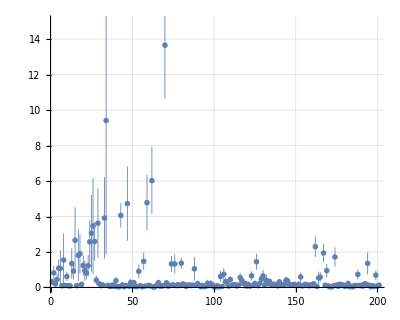

```mathematica
meanCrossEntropy=ParallelTable[Information[GP[[i]]]["MeanCrossEntropy"],{i,1,Length[GP]}];
SetOptions[$FrontEndSession,PrintingStyleEnvironment->"Working"]
meanCrossEntropyLossPlot=ListPlot[meanCrossEntropy,PlotRange->{{0,200},{0,15}},AxesStyle->Black,GridLines->Automatic,IntervalMarkersStyle->Thickness[0.0015],PlotMarkers->{Automatic,0.013},TicksStyle->Directive[FontSize->12.5],PlotRangePadding->0,AspectRatio->0.8]
```

### Plot the f (energy) evaluation history

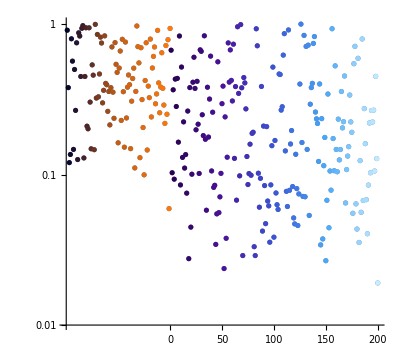

```mathematica
priorHistory=H[[All,2]][[1;;Length[energyData]]];
bayesianHistoryAll=H[[All,2]][[Length[energyData]+1;;]];
bayesianHistoryfmax=Cases[bayesianHistoryAll,x_/;x<=fmax];
Show[ListLogPlot[Table[Style[{i,bayesianHistoryAll[[i]]},ColorData["DeepSeaColors"][i/Length[bayesianHistoryAll]]],{i,1,Length[bayesianHistoryAll]}],PlotRange->{{1,Length[H]},{-6,Log[fmax]}},AxesOrigin->{-Length[priorHistory],0.01},GridLines->Automatic,Ticks->{{0,50,100,150,200},All}],ListLogPlot[Table[Style[{i-Length[priorHistory],priorHistory[[i]]},ColorData["RustTones"][i/Length[priorHistory]]],{i,1,Length[priorHistory]}],PlotRange->{{1,Length[H]},{-6,Log[fmax]}},AxesOrigin->{-Length[priorHistory],0.01},GridLines->Automatic,Ticks->{{0,50,100,150,200},All}],PlotRange->{{-Length[priorHistory],Length[H]-Length[priorHistory]},{-4.58,Log[fmax]}},AxesStyle->Black,PlotRangePadding->{{0,5},{0.1,0.1}},TicksStyle->Directive[FontSize->10.5],AspectRatio->0.9]
```

### Performance evaluation: Comparison of distributions to a random baseline

```mathematica
nSamplesRandomComp=3000; 
nSamplesRandomCompFinal=1000;
```

```mathematica
energyDataRandomCompArray={};
Do[
SeedRandom[RandomInteger[{1,10^9}],Method->All];
samplesRandomComp=BlockRandom[SeedRandom[RandomInteger[{1,10^9}],Method->{"MKL",Method->{"Sobol","Dimension"->10}}];
RandomPoint[Cuboid[Pmin,Pmax],nSamplesRandomComp]];
samplesRandomComp=MapAt[Round,#,{{8},{9}}]&/@samplesRandomComp;
SetSharedVariable[j];
γminArrayRandomComp={};
ptsGlobalRandomComp={};
SetSharedVariable[γminArrayRandomComp];
SetSharedVariable[ptsGlobalRandomComp];
j=0;
ξ=100;
energyGeomAndFibersRandomComp=Monitor[ParallelTable[j++;Flatten[{Table[samplesRandomComp[[i]][[k]],{k,1,Length[Pmin]}],
{optimalEnergyForGeometryRandomCompTwoRing[JMax,ξ,controlObjectiveType,rTarget,ΔZconstr,onlyNegativeγ,maxγMag,UMax,L,{samplesRandomComp[[i]][[1]],samplesRandomComp[[i]][[1]]+samplesRandomComp[[i]][[2]]},{samplesRandomComp[[i]][[1]]+samplesRandomComp[[i]][[2]],samplesRandomComp[[i]][[1]]+samplesRandomComp[[i]][[2]]+samplesRandomComp[[i]][[3]]},filled,EE,ν,{samplesRandomComp[[i]][[4]],samplesRandomComp[[i]][[5]]},{samplesRandomComp[[i]][[6]],samplesRandomComp[[i]][[7]]},{samplesRandomComp[[i]][[8]],samplesRandomComp[[i]][[9]]},{θ01,samplesRandomComp[[i]][[10]]}]}},1],{i,1,nSamplesRandomComp}],N[j/nSamplesRandomComp*100]];
γminArrayGoodControlRandomComp=Cases[γminArrayRandomComp,x_/;(x[[3]]==False&&x[[4]]<=fmax)];
energyGoodControlRandomComp=Cases[energyGeomAndFibersRandomComp,e_/;Last[e][[1]]==False];
energyGoodControlRandomComp=Cases[energyGeomAndFibersRandomComp,e_/;Last[e][[2]]<=fmax];
energyGoodControlRandomComp=Table[Flatten[{Table[energyGoodControlRandomComp[[i]][[j]],{j,1,Length[Pmin]}],Last[energyGoodControlRandomComp[[i]]][[2]]}],{i,1,Length[energyGoodControlRandomComp]}];
energyDataRandomComp=ParallelTable[energyGoodControlRandomComp[[i]][[1;;Length[Pmin]]]->Last[energyGoodControlRandomComp[[i]]],{i,1,Length[energyGoodControlRandomComp]}];
energyDataRandomComp=energyDataRandomComp[[1;;nSamplesRandomCompFinal]];
AppendTo[energyDataRandomCompArray,energyDataRandomComp],
{1}];
```

```mathematica
priorHistory=H[[All,2]][[1;;Length[energyData]]];
bayesianHistoryAll=H[[All,2]][[Length[energyData]+1;;]];
bayesianHistoryfmax=Cases[bayesianHistoryAll,x_/;x<=fmax];
```

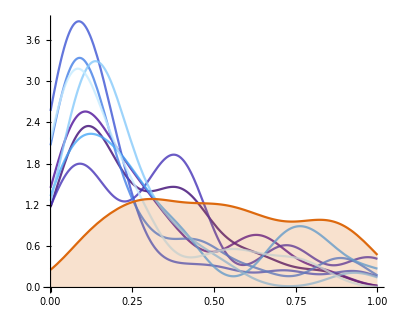

```mathematica
kernelDistrArray=Table[SmoothKernelDistribution[Partition[bayesianHistoryfmax,25][[i]],0.08],{i,1,Length[Partition[bayesianHistoryfmax,25]]}];
kernelDistrArray=Table[TruncatedDistribution[{0,fmax},kernelDistrArray[[i]]],{i,1,Length[kernelDistrArray]}];
kernelDistrPlots=Table[Plot[PDF[kernelDistrArray[[i]]][f],{f,0,fmax},PlotStyle->Directive[Opacity[0.8],ColorData["DeepSeaColors"][i/Length[kernelDistrArray]]]],{i,1,Length[kernelDistrArray]}];

kernelDistrRandom=TruncatedDistribution[{0,fmax},SmoothKernelDistribution[energyDataRandomComp[[All,2]],0.08]];
distributions=Show[kernelDistrPlots,Plot[PDF[kernelDistrRandom][f],{f,0,fmax},Filling->0,PlotStyle->ColorData["RustTones"][0.7]],PlotRange->All,AxesStyle->Black,TicksStyle->Directive[FontSize->12.5],AspectRatio->0.8]
```

```mathematica
BarLegend["DeepSeaColors",Subdivide[0,1,8],Ticks->None,LegendLayout->"Row"]
```

### Performance evaluation: Performance metrics compared to the random baseline

```mathematica
nCompare=Length[bayesianHistoryAll];
randomMinArray=Table[Table[Min[energyDataRandomCompArray[[randomRunI]][[All,2]][[1;;i]]],{i,1,nCompare}],{randomRunI,1,Length[energyDataRandomCompArray]}];
randomMinArrayAvg=Table[Mean[randomMinArray[[All,i]]],{i,1,nCompare}];
bayesianHistoryMinAll=Table[Min[bayesianHistoryAll[[1;;i]]],{i,1,nCompare}];
bayesianHistoryMinArray={bayesianHistoryMinAll};
```

```mathematica
fmaxThresholds=Table[fmaxThr,{fmaxThr,0.005,0.5*fmax,0.0005}];
fmaxThresholdIndicesRandomMinArray=Table[{fmaxThr,First[Flatten[Position[randomMinArray[[arrayInd]],x_/;x<=fmaxThr]]]},{arrayInd,1,Length[randomMinArray]},{fmaxThr,fmaxThresholds}];
minMaxFmaxThresholdIndex=Min[Table[Length[fmaxThresholdIndicesRandomMinArray[[i,All,2]]],{i,1,Length[randomMinArray]}]];
fmaxThresholdIndicesRandomMinArrayAvg=Table[{fmaxThresholds[[i]],Ceiling[Mean[fmaxThresholdIndicesRandomMinArray[[All,i,2]]]]},{i,1,Length[fmaxThresholds]}];

fmaxThresholdIndicesBayesian=Table[{fmaxThr,First[Flatten[Position[bayesianHistoryMinArray[[arrayInd]],x_/;x<=fmaxThr]]]},{arrayInd,1,Length[bayesianHistoryMinArray]},{fmaxThr,fmaxThresholds}];
minMaxFmaxThresholdIndexBayesian=Min[Table[Length[fmaxThresholdIndicesBayesian[[i,All,2]]],{i,1,Length[bayesianHistoryMinArray]}]];
fmaxThresholdIndicesBayesianAvg=Table[{fmaxThresholds[[i]],Ceiling[Mean[fmaxThresholdIndicesBayesian[[All,i,2]]]]},{i,1,Length[fmaxThresholds]}];
```

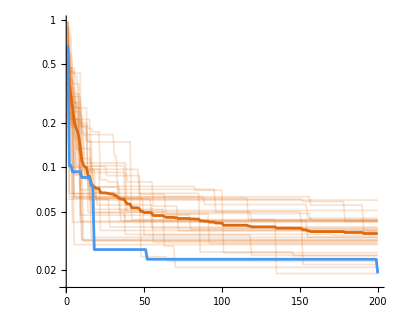

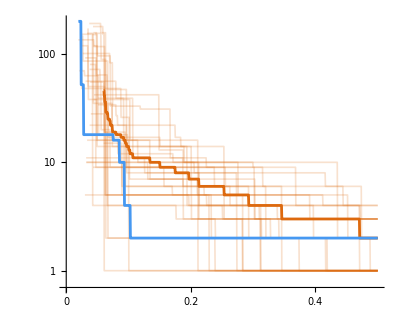

```mathematica
runningMin[x_]:=Module[{xmin,minList,oldxmin,minListWithOld},
xmin=Infinity;
minList={};
minListWithOld={};
Do[If[x[[i]]<xmin,oldxmin=xmin;xmin=x[[i]];AppendTo[minListWithOld,{i,oldxmin}];AppendTo[minListWithOld,{i,xmin}];AppendTo[minList,{i,xmin}],{}],{i,1,Length[x]}];
{minList,minListWithOld}
];

ListLinePlot[Flatten[{randomMinArray,{randomMinArrayAvg},{bayesianHistoryMinAll}},1],PlotStyle->Flatten[{Table[Directive[Thickness[0.003],Opacity[0.2],ColorData["RustTones"][0.7]],{i,1,Length[energyDataRandomCompArray]}],Directive[Thickness[0.005],ColorData["RustTones"][0.7]],Directive[Thickness[0.005],ColorData["DeepSeaColors"][0.7]]}],PlotRange->All,ScalingFunctions->"Log",AspectRatio->0.8,AxesStyle->Black,TicksStyle->Directive[FontSize->12.5]]
ListLinePlot[Flatten[{fmaxThresholdIndicesRandomMinArray,{fmaxThresholdIndicesRandomMinArrayAvg},fmaxThresholdIndicesBayesian},1],PlotRange->All,ScalingFunctions->{"Linear","Log"},PlotStyle->Flatten[{Table[Directive[Thickness[0.003],Opacity[0.2],ColorData["RustTones"][0.7]],{i,1,Length[fmaxThresholdIndicesRandomMinArray]}],Directive[Thickness[0.005],ColorData["RustTones"][0.7]],Directive[Thickness[0.005],ColorData["DeepSeaColors"][0.7]]}],AspectRatio->0.8,AxesStyle->Black,PlotRangePadding->{{0,Automatic},{Automatic,Automatic}},AxesOrigin->{0,0.7},TicksStyle->Directive[FontSize->12.5]]
```

### Plot the evaluation history for the J cost function at each f evaluation

```mathematica
nSamples=400; 
nSamplesFinal=100;

SeedRandom[RandomInteger[{1,10^9}],Method->All];
samples=BlockRandom[SeedRandom[RandomInteger[{1,10^9}],Method->{"MKL",Method->{"Sobol","Dimension"->10}}];
RandomPoint[Cuboid[Pmin,Pmax],nSamples]];
samplesNonRounded=samples;
samples=MapAt[Round,#,{{8},{9}}]&/@samples;
```

```mathematica
SetSharedVariable[j]
γminArray={};
ptsGlobalPrior={};
SetSharedVariable[γminArray];
SetSharedVariable[ptsGlobalPrior];
j=0;
ξ=100;
energyGeomAndFibers=Monitor[ParallelTable[j++;Flatten[{Table[samplesNonRounded[[i]][[k]],{k,1,Length[Pmin]}],
{optimalEnergyForGeometryInitialTwoRing[i,JMax,ξ,controlObjectiveType,rTarget,ΔZconstr,onlyNegativeγ,maxγMag,UMax,L,{samples[[i]][[1]],samples[[i]][[1]]+samples[[i]][[2]]},{samples[[i]][[1]]+samples[[i]][[2]],samples[[i]][[1]]+samples[[i]][[2]]+samples[[i]][[3]]},filled,EE,ν,{samples[[i]][[4]],samples[[i]][[5]]},{samples[[i]][[6]],samples[[i]][[7]]},{samples[[i]][[8]],samples[[i]][[9]]},{θ01,samples[[i]][[10]]}]}},1],{i,1,nSamples}],N[j/nSamples*100]];
```

```mathematica
sortedPtsPriorIndices=Ordering[ptsGlobalPrior[[All,1]]];
sortedPtsGlobalPrior=ptsGlobalPrior[[All,2]][[sortedPtsPriorIndices]];
```

```mathematica
indicesSatisfyingFmaxPriors=Flatten[Position[energyGeomAndFibers[[All,11]][[All,2]],_?(#<=fmax&)]];
indicesWithGoodControlPriors=Flatten[Position[energyGeomAndFibers[[All,11]][[All,1]],_?(#==False&)]];
Length[indicesWithGoodControlPriors]
indicesFinalPriors=Intersection[indicesSatisfyingFmaxPriors,indicesWithGoodControlPriors];
Length[indicesFinalPriors]
indicesFinalPriors=indicesFinalPriors[[1;;nSamplesFinal]];
ptsGlobalPriorAfterDiscarding=sortedPtsGlobalPrior[[indicesFinalPriors]];
```

```mathematica
plotStyles=Table[Directive[PointSize[0.005],Opacity[0.5],ColorData["RustTones"][i/Length[ptsGlobalPriorAfterDiscarding]]],{i,1,Length[ptsGlobalPriorAfterDiscarding]}];
```

```mathematica
plotData=ParallelTable[ptsGlobalPriorAfterDiscarding[[i]][[All,2]],{i,1,Length[ptsGlobalPriorAfterDiscarding]}];
```

#### For the priors

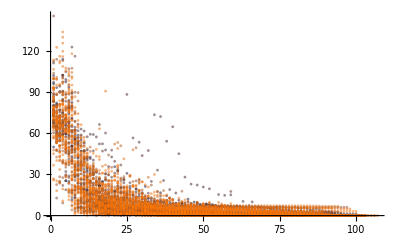

```mathematica
priorJ=ListPlot[plotData,PlotStyle->plotStyles,PlotRange->All,AxesOrigin->{0,0},PlotRangePadding->{Scaled[.01],0},TicksStyle->Directive[FontSize->15],AspectRatio->0.6]
```

#### For the Bayesian optimization iterations

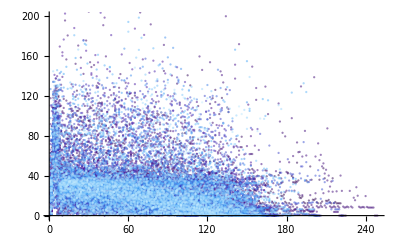

```mathematica
JBayesian=Show[Table[ListPlot[ptsGlobalBayesian[[i]][[All,2]],PlotStyle->Directive[Opacity[0.5],PointSize[0.004],ColorData["DeepSeaColors"][i/Length[ptsGlobalBayesian]]],PlotRange->{Automatic,{0,400}}],{i,1,Length[ptsGlobalBayesian]}],PlotRange->{All,{0,200}},TicksStyle->Directive[FontSize->15],AspectRatio->0.6]
```

### Investigate the erratic multi-valuedness of the objective function

```mathematica
nSamplesRandomCompSingleRing=300; 
repeats=10;
dim=2;

αList=Subdivide[Pi/12,Pi/4,5];
SeedRandom[RandomInteger[{1,10^9}],Method->All];
samplesRandomCompSingleRing=Table[{Flatten[ParallelTable[SeedRandom[RandomInteger[{1,10^9}],Method->All];BlockRandom[SeedRandom[RandomInteger[{1,10^9}],Method->{"MKL",Method->{"Sobol","Dimension"->dim}}];
Flatten[RandomPoint[Cuboid[{0.2},{0.5}],nSamplesRandomCompSingleRing],1]],{i,1,repeats}],1],α},{α,αList}];
```

```mathematica
SetSharedVariable[j]
j=0;
ξ=100;

energyGeomAndFibersSingleRing=ParallelTable[{samplesRandomCompSingleRing[[I]][[1]][[i]],samplesRandomCompSingleRing[[I]][[2]],
optimalEnergyForGeometryRandomCompSingleRing[JMax,ξ,controlObjectiveType,rTarget,ΔZconstr,onlyNegativeγ,maxγMag,UMax,L,samplesRandomCompSingleRing[[I]][[1]][[i]],samplesRandomCompSingleRing[[I]][[1]][[i]]+0.1,filled,EE,ν,samplesRandomCompSingleRing[[I]][[2]],σ,Nγ,θ0]},{I,1,Length[αList]},{i,1,repeats*nSamplesRandomCompSingleRing}];
```

```mathematica
energyGoodControlSingleRing=ParallelTable[Cases[energyGeomAndFibersSingleRing[[I]],e_/;Last[e][[1]]==False],{I,1,Length[αList]}];
energyGoodControlSingleRing=Table[Flatten[{Table[energyGoodControlSingleRing[[I]][[i]][[j]],{j,1,dim}],Last[energyGoodControlSingleRing[[I]][[i]]][[2]]}],{I,1,Length[αList]},{i,1,Length[energyGoodControlSingleRing[[I]]]}];
energyDataSingleRing=ParallelTable[energyGoodControlSingleRing[[I]][[i]][[1;;dim]]->Last[energyGoodControlSingleRing[[I]][[i]]],{I,1,Length[αList]},{i,1,Length[energyGoodControlSingleRing[[I]]]}];
energyDataForPlot=ParallelTable[Flatten[{energyDataSingleRing[[I]][[i]][[1,1;;2]],energyDataSingleRing[[I]][[i]][[2]]},1],{I,1,Length[αList]},{i,1,Length[energyDataSingleRing[[I]]]}];
```

```mathematica
energyDataForPlotNormalized=ParallelTable[{energyDataForPlot[[I]][[All,1]][[i]]/L,energyDataForPlot[[I]][[All,3]][[i]]},{I,1,Length[energyDataForPlot]},{i,1,Length[energyDataForPlot[[I]]]}];
```

```mathematica
energyPlots=Table[ListLogPlot[energyDataForPlotNormalized[[3*i+j]],Frame->True,FrameTicks->{{Automatic,None},{Charting`ScaledTicks["Linear"][0.1/L,0.6/L,{6,5}],None}},AspectRatio->Automatic,AxesStyle->Black,FrameStyle->Black,PlotRangePadding->{.025/L,0.5},PlotRange->{{0.2/L,0.5/L},If[i==0,{10^(-2),10},{10^(-2),10}]},PlotMarkers->{Automatic,0.006}],{i,0,1},{j,1,3}];
```

### Plot the best actuator design and its deformation when reaching the control objective

```mathematica
{rPar,dPar,γList,ζHatSym,u1HatSym,u2HatSym,u3HatSym}=filamentSetup[L,{Pbest[[1]],Pbest[[1]]+Pbest[[2]]},{Pbest[[1]]+Pbest[[2]],Pbest[[1]]+Pbest[[2]]+Pbest[[3]]},filled,EE,ν,{Pbest[[4]],Pbest[[5]]},{Pbest[[6]],Pbest[[7]]},Round[{Pbest[[8]],Pbest[[9]]}],{θ01,Pbest[[10]]}];
```

```mathematica
γmin={Last[Last[ptsGlobalBayesian]][[1]][[1;;Round[Pbest[[8]]]]],Last[Last[ptsGlobalBayesian]][[1]][[Round[Pbest[[8]]]+1;;]]}
```

{{-1.52948,0.918195,-0.0139759},{2.1858,-0.966592,-0.278078,1.65315}}

```mathematica
rVal=centerlineVal[rPar,γmin,Z]
ParametricPlot3D[rVal,{Z,0,L}]
```

{InterpolatingFunction[…][Z],InterpolatingFunction[…][Z],InterpolatingFunction[…][Z]}

-Graphics3D-

Other plots

```mathematica
coordLinesTarget={Graphics3D[Line[{{0,0,0},{5,0,0}}]],
Graphics3D[Line[{{0,0,0},{0,5,0}}]],
Graphics3D[{Dashed,Line[{{rTarget[[1]],0,0},{rTarget[[1]],rTarget[[2]],0}}]}],
Graphics3D[{Dashed,Line[{{0,rTarget[[2]],0},{rTarget[[1]],rTarget[[2]],0}}]}],
Graphics3D[{Dashed,Line[{{rTarget[[1]],rTarget[[2]],0},rTarget}]}]};
targetPlot=Graphics3D[{targetColor,Sphere[rTarget,0.2]}];
```

Full plot

```mathematica
intermediatePlots=ParallelTable[ParametricPlot3D[centerlineVal[rPar,γ0[[i]]*γmin,Z],{Z,0,L},PlotStyle->Directive[colors[[1]],Opacity[0.15],CapForm["Butt"]],Method->{"TubePoints"->60},PlotPoints->100,PlotRange->All]/. Line[pts_,rest___]:>Tube[pts,Total[Pbest[[1;;3]]],rest],{i,1,Length[γ0]}]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
ϕ2={0,0}
```

```mathematica
rodPlotFullReference=rodPlotFullListNonTapered[rPar,dPar,{0,0,0,0,0,0,0},0,L,ϕ2,Pbest[[4;;5]],{Pbest[[1]],Pbest[[1]]+Pbest[[2]]},{Pbest[[1]]+Pbest[[2]],Pbest[[1]]+Pbest[[2]]+Pbest[[3]]},{θ01,Pbest[[10]]},Pbest[[6;;7]],Round[{Pbest[[8]],Pbest[[9]]}],filled,{Blend[{Gray,Black},0.5],Blend[{Gray,White},0.4]},{Red,Orange},{1,0.4},fiberSectionOpacity];
```

```mathematica
rodPlotFullReferenceRing1=rodPlotFullListNonTapered[rPar,dPar,{0,0,0,0,0,0,0},0,L,{0},{Pbest[[4]]},{Pbest[[1]]},{Pbest[[1]]+Pbest[[2]]},{θ01},{Pbest[[6]]},Round[{Pbest[[8]]}],filled,{Blend[{Gray,Black},0.5]},{Red},{1},{fiberSectionOpacity[[1]]}];
```

```mathematica
rodPlotFullReferenceRing2=rodPlotFullListNonTapered[rPar,dPar,{0,0,0,0,0,0,0},0,L,{0},{Pbest[[5]]},{Pbest[[1]]+Pbest[[2]]},{Pbest[[1]]+Pbest[[2]]+Pbest[[3]]},{Pbest[[10]]},{Pbest[[7]]},Round[{Pbest[[9]]}],False,{Blend[{Gray,White},0.5]},{Orange},{1},{fiberSectionOpacity[[1]]}];
```

```mathematica
rodPlotFull=rodPlotFullListNonTapered[rPar,dPar,γmin,0,L,ϕ2,Pbest[[4;;5]],{Pbest[[1]],Pbest[[1]]+Pbest[[2]]},{Pbest[[1]]+Pbest[[2]],Pbest[[1]]+Pbest[[2]]+Pbest[[3]]},{θ01,Pbest[[10]]},Pbest[[6;;7]],Round[{Pbest[[8]],Pbest[[9]]}],filled,{Blend[{Gray,Black},0.5],Blend[{Gray,White},0.4]},{Red,Orange},{1,0.4},fiberSectionOpacity];
```

```mathematica
specularity=0.5;
specularityExponent=4;
plotPoints=40;
```

```mathematica
rodPlotRing1=Show[rodPlotFullReferenceRing1,Ticks->None,Axes->False,PlotRange->{{-3,5},{-3,5},{0,L}},Boxed->False,Lighting->Automatic,PlotRangePadding->0,ImagePadding->0,Method->{"ShrinkWrap"->True}]
```

-Graphics3D-

```mathematica
rodPlotRing2=Show[rodPlotFullReferenceRing2,Ticks->None,Axes->False,PlotRange->{{-3,5},{-3,5},{0,L}},Boxed->False,Lighting->Automatic,PlotRangePadding->0,ImagePadding->0,Method->{"ShrinkWrap"->True}]
```

-Graphics3D-